# Numerical implementation of the Z function

This implemetation uses the representation in terms of error functions for small argument |z|<M and asymptotic expansion for argument |z| > M. Now M=4. 
Note: The choice of s in the asymptotic expansion is different from that given in the plasma formulary (their sigma).  Use of their sigma clearly doesn't work for example when Re[z] =0.  Then sigma must be 0 whereas their forumla would have sigma=1.

### Z function module

```mathematica
Zfun[z0_]:=Module[{M=5.,s,y,q,z2},
z=N[z0];
If[Abs[z]<M,

1.772453851*I* E^(-z^2)(1+ Erf[I z]),	(* error function form  *)
	
	y=Im[z];	(* asymptotic expansion *)
	Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
	z2=z^2;
	q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
	1.772453851*I*s*E^(-z2)-q		(* end of asymptotic expansion *)
]	(* end if  *)
]	(* end module *)
```

### Testing of Zfun

```mathematica
Zfun[1+I]
```

-0.369058 + 0.540145 I

```mathematica
x={0,.1,1,2,5};
y={.1,2,5};
TableForm[Table[Zfun[x[[i]]+y[[j]]*I],{i,1,5},{j,1,3}]]
```

0.+1.58893 ⅈ | 0.+0.452677 ⅈ | 0.+0.196219 ⅈ
-0.167198+1.57479 ⅈ | -0.0189018+0.451937 ⅈ | -0.00377991+0.196148 ⅈ
-0.954564+0.661427 ⅈ | -0.164834+0.387268 ⅈ | -0.0365201+0.189294 ⅈ
-0.587715+0.0712551 ⅈ | -0.23251+0.262239 ⅈ | -0.0662039+0.171038 ⅈ
-0.204176+0.00426596 ⅈ | -0.173678+0.0720393 ⅈ | -0.0989716+0.100969 ⅈ

Test timing for 100 evaluations

```mathematica
Table[Zfun[.1*i*E^(.1*I*i)],{i,0,100}];
```

Time was 8.4 sec

### Testing of individual parts

```mathematica
Zf[z_]:=1.772453851*I* E^(-z^2)(1+ Erf[I z])//N
```

```mathematica
Zf[.1*I]
```

1.58893 I

```mathematica
TableForm[Table[Zf[i+j*I],{i,0,4,2},{j,-2,2,2}]]
```

193.093 I                1.77245 I                    0.452677 I

-3.73969 - 0.778024 I    -0.602681 + 0.0324636 I      -0.23251 + 0.262239 I

                                               -7
-0.200653 - 0.105813 I   -0.258696 + 1.99463 10   I   -0.20066 + 0.105792 I

These agree to printed accuracy with the Z function tables

Check Symmetry

```mathematica
fsym[z_]:=(Zf[Conjugate[z]]+Conjugate[Zf[-z]])/Abs[Zf[Conjugate[z]]]
```

```mathematica
TableForm[Table[fsym[i+j*I],{i,0,4,2},{j,-2,2,2}]]
```

0. I        0. I        0. I

0. + 0. I   0. + 0. I   0. + 0. I

0. + 0. I   0. + 0. I   0. + 0. I

```mathematica
ZAsymp[z_]:=Module[{s,a,y,q,z2},
			a=Abs[Re[z]];
			y=Im[z];
			Which[y==0.,s=1,  y>0,s=0,   y<0,s=2];
			z2=z^2;
			q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
			N[1.772453851*I*s*E^(-z2)-q]
			]
```

```mathematica
TableForm[Table[ZAsymp[i+j*ⅈ],{i,2,8,2},{j,-5,5,5}]]
```

-4.26809×10^9+1.90782×10^9 ⅈ | -0.613403+0.0324636 ⅈ | -0.0662039+0.171038 ⅈ
-21403.2-19157.7 ⅈ | -0.258684+1.99463×10^-7 ⅈ | -0.095837+0.122718 ⅈ
-0.097803-0.0829283 ⅈ | -0.169085+4.11125×10^-16 ⅈ | -0.097821+0.0828719 ⅈ
-0.0898156-0.0567752 ⅈ | -0.126+2.84268×10^-28 ⅈ | -0.0898156+0.0567752 ⅈ

This also checks with Z function table

Check Symmetry

```mathematica
fsym[z_]:=(ZAsymp[Conjugate[z]]+Conjugate[ZAsymp[-z]])/Abs[ZAsymp[Conjugate[z]]]
```

```mathematica
TableForm[Table[fsym[i+j*I],{i,-4,8,.51},{j,-5,5,2.5}]]
```

0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ

```mathematica
r=1.
t1=Table[{theta,Zf[r*Exp[I*theta]]},{theta,0.,2 Pi,.05 Pi//N}];
```

1.

```mathematica
CmplxListPlot[t1,"theta","Zfun",PlotRange->All]
```

-Graphics-

Check agreement between Erf form and asymptotic expansion at overlap

```mathematica
r=4.
t1=Table[{theta,Zf[r*Exp[I*theta]]},{theta,0.,2 Pi,.05 Pi//N}];
t2=Table[{theta,ZAsymp[r*Exp[I*theta]]},{theta,0.,2 Pi,.05 Pi//N}];
```

4.

```mathematica
CmplxListPlot[t1,"theta","Zfun",PlotRange->All]
CmplxListPlot[t1,"theta","Zfun",PlotRange->{0,.2}]
```

-Graphics-

-Graphics-

```mathematica
CmplxListPlot[t2,"theta","Zfun",PlotRange->All]
CmplxListPlot[t2,"theta","Zfun",PlotRange->{0.,.2}]
```

-Graphics-

```mathematica
t4=Abs[t1];
t5=Transpose[{Transpose[t1][[1]],Transpose[t1-t2][[2]]}];
```

```mathematica
CmplxListPlot[t5,"theta","Zfun",PlotRange->All]
```

At |z|=4 both methods agree to about 10^-5. Check relative error

```mathematica
t6=Transpose[{Transpose[t4][[1]],MapThread[Divide,{Transpose[t5][[2]],Transpose[t4][[2]]}]}]
```

-17
{{0., -0.0000448625 + 6.12323 10    I}, {0.15708, 0.0000145713 + 0.0000380882 I}, 
 
  {0.314159, 0.0000292427 - 0.0000209623 I}, {0.471239, -0.0000232983 - 0.0000218092 I}, 
 
  {0.628319, -0.0000161291 + 0.0000237888 I}, {0.785398, 0.0000235328 + 0.0000118432 I}, 
 
                       -6                                                        -6
  {0.942478, 8.54757 10   - 0.0000230415 I}, {1.09956, -0.0000225471 - 5.92292 10   I}, 
 
                       -6                                                      -6
  {1.25664, -3.73421 10   + 0.0000221533 I}, {1.41372, 0.0000219039 + 1.8065 10   I}, 
 
                     -20                                                       -6
  {1.5708, 1.40596 10    - 0.0000218199 I}, {1.72788, -0.0000219039 + 1.8065 10   I}, 
 
                      -6                                                       -6
  {1.88496, 3.73421 10   + 0.0000221533 I}, {2.04204, 0.0000225471 - 5.92292 10   I}, 
 
                       -6
  {2.19911, -8.54757 10   - 0.0000230415 I}, {2.35619, -0.0000235328 + 0.0000118432 I}, 
 
  {2.51327, 0.0000161291 + 0.0000237888 I}, {2.67035, 0.0000232983 - 0.0000218092 I}, 
 
  {2.82743, -0.0000292427 - 0.0000209623 I}, {2.98451, -0.0000145713 + 0.0000380882 I}, 
 
                                     -7
  {3.14159, 0.0000448625 + 7.71034 10   I}, {3.29867, -0.0000145713 - 0.0000380883 I}, 
 
  {3.45575, -0.0000292424 + 0.000020962 I}, {3.61283, 0.0000233015 + 0.0000218122 I}, 
 
                                                                 -6             -7
  {3.76991, 0.0000147662 - 0.0000217786 I}, {3.92699, -1.59661 10   - 8.03518 10   I}, 
 
                       -9             -8                         -10             -11
  {4.08407, -4.24401 10   + 1.14405 10   I}, {4.24115, 1.28499 10    + 3.37555 10    I}, 
 
                      -13             -12                          -13             -14
  {4.39823, 6.14162 10    - 3.64337 10    I}, {4.55531, -3.70061 10    - 3.05365 10    I}, 
 
                       -28             -13                         -13             -14
  {4.71239, -3.25196 10    + 1.68168 10    I}, {4.86947, 3.69932 10    - 3.05042 10    I}, 
 
                       -13             -12                          -10             -11
  {5.02655, -6.14162 10    - 3.64337 10    I}, {5.18363, -1.28499 10    + 3.37557 10    I}, 
 
                      -9             -8                         -6             -7
  {5.34071, 4.24401 10   + 1.14405 10   I}, {5.49779, 1.59661 10   - 8.03518 10   I}, 
 
  {5.65487, -0.0000147662 - 0.0000217786 I}, {5.81195, -0.0000233015 + 0.0000218122 I}, 
 
  {5.96903, 0.0000292424 + 0.000020962 I}, {6.12611, 0.0000145713 - 0.0000380883 I}, 
 
                                      -7
  {6.28319, -0.0000448625 - 7.71034 10   I}}

```mathematica
CmplxListPlot[t6,"theta","Zfun",PlotRange->All]
```

-Graphics-

Things are not quite so rosy at z|=10

```mathematica
r=10.
t1=Table[{theta,Zf[r*Exp[I*theta]]},{theta,0.,2 Pi,.05 Pi//N}]//N;
t2=Table[{theta,ZAsymp[r*Exp[I*theta]]},{theta,0.,2 Pi,.05 Pi//N}]//N;
```

10.

```mathematica
CmplxListPlot[t1,"theta","Zfun",PlotRange->{0,.2}]
```

-Graphics-

```mathematica
CmplxListPlot[t2,"theta","Zfun",PlotRange->{0.,.2}]
```

-Graphics-

There seems to be a problem with the Erf function form for Arg[z] in (1,2)

```mathematica
t4=Abs[t1];
t5=Transpose[{Transpose[t1][[1]],Transpose[t1-t2][[2]]}];
```

```mathematica
CmplxListPlot[t5,"theta","Zfun",PlotRange->All]
```

-Graphics-

At |z|=4 both methods agree to about 10^-5. Check relative error

```mathematica
t6=Transpose[{Transpose[t4][[1]],MapThread[Divide,{Transpose[t5][[2]],Transpose[t4][[2]]}]}]
```

-9             -17                         -10             -9
{{0., -3.16448 10   + 6.12323 10    I}, {0.15708, 4.88693 10    + 3.06303 10   I}, 
 
                       -9             -9                           -9             -9
  {0.314159, 2.84109 10   - 1.03428 10   I}, {0.471239, -1.55139 10   - 2.61628 10   I}, 
 
                        -9             -9                          -9             -9
  {0.628319, -2.36769 10   + 1.91821 10   I}, {0.785398, 2.15768 10   + 2.00447 10   I}, 
 
  {0.942478, 0.0110157 + 0.00952446 I}, {1.09956, 2.17644 - 2.20134 I}, 
 
  {1.25664, 1.15444 - 0.894229 I}, {1.41372, 1.31209 - 2.3226 I}, 
 
                                 13
  {1.5708, -0.995073 - 8.12539 10   I}, {1.72788, -1.31209 - 2.3226 I}, 
 
  {1.88496, -1.15444 - 0.894229 I}, {2.04204, -2.17644 - 2.20134 I}, 
 
                                                             -9             -9
  {2.19911, -0.0110157 + 0.00952446 I}, {2.35619, -2.15768 10   + 2.00447 10   I}, 
 
                      -9             -9                         -9             -9
  {2.51327, 2.36769 10   + 1.91821 10   I}, {2.67035, 1.55139 10   - 2.61627 10   I}, 
 
                       -9             -9                          -10             -9
  {2.82743, -2.84109 10   - 1.03428 10   I}, {2.98451, -4.88707 10    + 3.06302 10   I}, 
 
                      -9             -16                          -10             -9
  {3.14159, 3.16448 10   - 1.60812 10    I}, {3.29867, -4.88707 10    - 3.06302 10   I}, 
 
                       -9             -9                         -9             -9
  {3.45575, -2.84111 10   + 1.03428 10   I}, {3.61283, 1.55139 10   + 2.61628 10   I}, 
 
                      -9             -9                          -11             -11
  {3.76991, 2.36769 10   - 1.91821 10   I}, {3.92699, -6.25721 10    - 5.81288 10    I}, 
 
                       -16             -17
  {4.08407, -1.67409 10    - 8.37043 10    I}, {4.24115, 0. + 0. I}, {4.39823, 0. + 0. I}, 
 
  {4.55531, 0. + 0. I}, {4.71239, 0. + 0. I}, {4.86947, 0. + 0. I}, {5.02655, 0. + 0. I}, 
 
                                                 -17
  {5.18363, 0. + 0. I}, {5.34071, 0. - 8.37043 10    I}, 
 
                      -11             -11                          -9             -9
  {5.49779, 6.25721 10    - 5.81288 10    I}, {5.65487, -2.36769 10   - 1.91821 10   I}, 
 
                       -9             -9                         -9             -9
  {5.81195, -1.55139 10   + 2.61628 10   I}, {5.96903, 2.84111 10   + 1.03428 10   I}, 
 
                      -10             -9                          -9             -17
  {6.12611, 4.88707 10    - 3.06302 10   I}, {6.28319, -3.16448 10   + 3.83476 10    I}}

```mathematica
CmplxListPlot[t6,"theta","Zfun",PlotRange->All]
```

-Graphics-

There is a particularly bad problem at Arg[z] = Pi/2 where the Erf form gives zero modulus

### What happens if we use the choice of s in the asymptotic expansion given in tha NRL formulary

```mathematica
ZAsymp2[z_Complex]:=Module[{s,a,y,q,z2},
			a=Abs[Re[z]];
			y=Im[z];
			Which[a==0.,s=1,  y>1/a,s=0,  Abs[y]<1/a,s=1,   y<-1/a,s=2];
			z2=z^2;
			q=(1+1/(2 z2)+3/(4 z2^2)+15/(8 z2^3)+7*15/(16 z2^4))/z;
			N[1.772453851*I*s*E^(-z2)-q]
			]
```

```mathematica
r=4.
t1=Table[{theta,Zf[r*Exp[I*theta]]},{theta,0.,2 Pi,.05 Pi//N}];
t2=Table[{theta,ZAsymp2[r*Exp[I*theta]]},{theta,0.,2 Pi,.05 Pi//N}];
```

4.

```mathematica
CmplxListPlot[t1,"theta","Zfun",PlotRange->All]
CmplxListPlot[t1,"theta","Zfun",PlotRange->{0,.3}]
```

-Graphics-

-Graphics-

```mathematica
CmplxListPlot[t2,"theta","Zfun",PlotRange->All]
CmplxListPlot[t2,"theta","Zfun",PlotRange->{0.,.3}]
```

-Graphics-

-Graphics-

There is a bogus spike in Zasymp2 at Arg[z]=Pi/2 also the spike at Arg[z]=3Pi/2 is half as big as it should be.  The behavior is clearly wrong for z=0+I*y.  I conclude that the perscription in the plasma formulary is wrong

## Plot stuff for real values of z

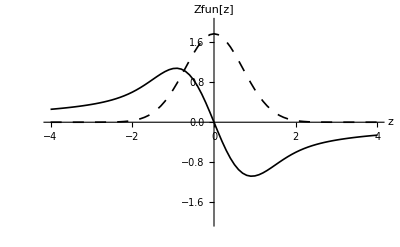

```mathematica
zf=Table[{z,Zfun[z]},{z,-4,4,.1}];
ComplexVectorListPlot[zf,"z","Zfun[z]", PlotRange->{-2,2}]
```

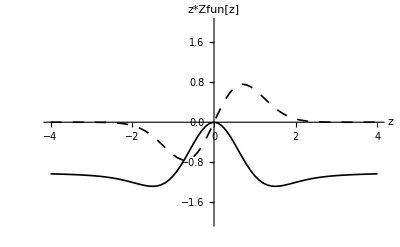

```mathematica
zf=Table[{z,z Zfun[z]},{z,-4,4,.1}];
ComplexVectorListPlot[zf,"z","z*Zfun[z]", PlotRange->{-2,2}]
```

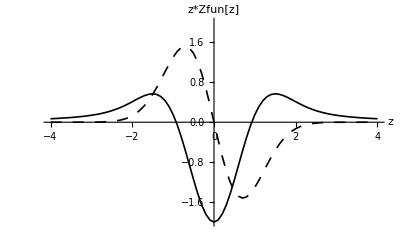

```mathematica
zf=Table[{z,-2(1.+z Zfun[z])},{z,-4,4,.1}];
ComplexVectorListPlot[zf,"z","z*Zfun[z]", PlotRange->{-2,2}]
```

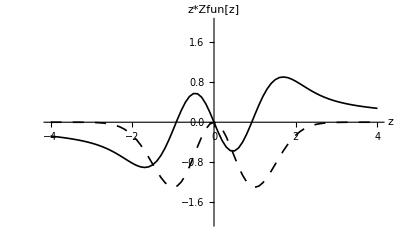

```mathematica
zf=Table[{z,-2 z(1.+z Zfun[z])},{z,-4,4,.1}];
ComplexVectorListPlot[zf,"z","z*Zfun[z]", PlotRange->{-2,2}]
```